```mathematica
<<madtomma`madinput`readinmadfiles2`
```

```mathematica
ReadInMADFile["LINAC_MERGER_BASE.MFF"]
```

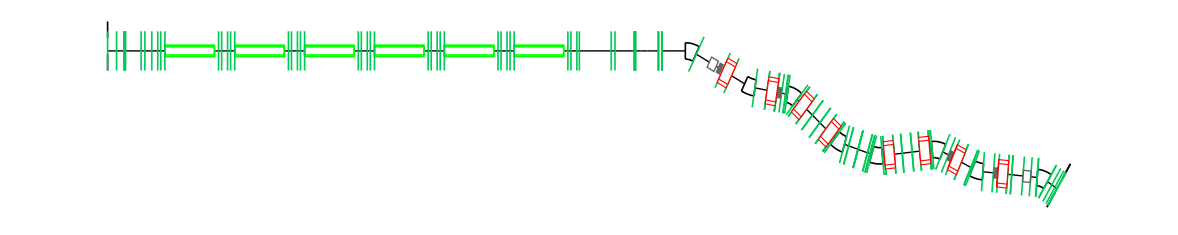

```mathematica
LAT//MADDraw
```

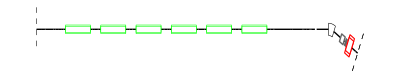

```mathematica
Select[LAT[[1;;133]],#[[3]]>0&]//MADDraw
```

```mathematica
beta0={1.06618806,-0.41056256,1.54074680,-0.91009982,0,0}
```

{1.06619,-0.410563,1.54075,-0.9101,0,0}

```mathematica
MADWrite["merge",LAT[[1;;133]],Slice->5];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
```

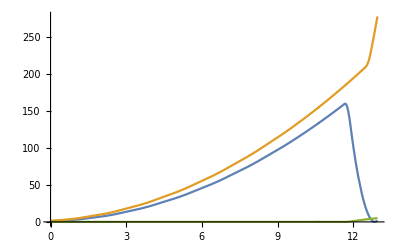

```mathematica
ListLinePlot[{Transpose[{S,BETX}],Transpose[{S,BETY}],Transpose[{S,10 DX}]},PlotRange->All]
```